```mathematica
Log[Tan[10Degree/2]]//N
```

-2.43625

```mathematica
Log[Tan[1Degree/2]]//N
```

-4.74135

```mathematica
Log[Tan[0.3Degree/2]]//N
```

-5.94534

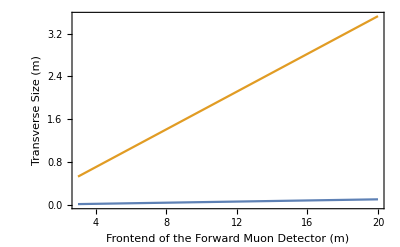

```mathematica
Plot[{x Tan[0.3Degree],x Tan[10Degree]},{x,3,20},Frame->True,FrameLabel->{"Frontend of the Forward Muon Detector (m)","Transverse Size (m)"}]
```

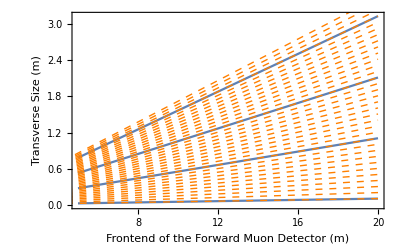

```mathematica
Show[
Plot[Table[x Tan[i],{i,0.3Degree,10Degree,0.05}],{x,5,20},Frame->True,FrameLabel->{"Frontend of the Forward Muon Detector (m)","Transverse Size (m)"},FrameStyle->Thick, BaseStyle->16,ImageSize->400],
Plot[Table[x Tan[i],{i,0.3Degree,10Degree,0.005}],{x,3,20},PlotStyle->{Thin,Dashed,Orange},Frame->True,FrameLabel->{"Frontend of the Forward Muon Detector (m)","Transverse Size (m)"}]
]
```